## Kronecker Product

```mathematica
A = {{a,b},{c,d}};
B= {{e,f},{g,h}};
KroneckerProduct[A,B]//MatrixForm
KroneckerProduct[B,A]//MatrixForm
```

(a e | a f | b e | b f
a g | a h | b g | b h
c e | c f | d e | d f
c g | c h | d g | d h)

(a e | b e | a f | b f
c e | d e | c f | d f
a g | b g | a h | b h
c g | d g | c h | d h)

## TFIM

```mathematica
zz = KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]/4;
tf = KroneckerProduct[PauliMatrix[0],PauliMatrix[1]]/2 + KroneckerProduct[PauliMatrix[1],PauliMatrix[0]]/2;
```

```mathematica
zz//MatrixForm
tf//MatrixForm
```

(1/4 | 0 | 0 | 0
0 | -1/4 | 0 | 0
0 | 0 | -1/4 | 0
0 | 0 | 0 | 1/4)

(0 | 1/2 | 1/2 | 0
1/2 | 0 | 0 | 1/2
1/2 | 0 | 0 | 1/2
0 | 1/2 | 1/2 | 0)

```mathematica
H2=-4 J zz -2 h tf;
H2//MatrixForm
{vals,vecs}=Eigensystem[H2];
```

(-1 | -h | -h | 0
-h | 1 | 0 | -h
-h | 0 | 1 | -h
0 | -h | -h | -1)

```mathematica
Det[H2-λ IdentityMatrix[4]]//FullSimplify
```

-((1+4 h^2-λ^2) (-1+λ^2))

1

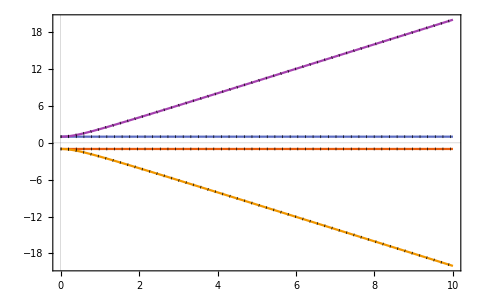

```mathematica
J=1
Plot[Evaluate@vals,{h,0,10},PlotTheme->"Scientific"];
Show[%,Plot[{+1,-1,√(4 h^2+1),-√(4 h^2+1)},{h,0,10},PlotStyle->{{Dotted,Black}}]]
```

```mathematica
tf
```

{{0,1/2,1/2,0},{1/2,0,0,1/2},{1/2,0,0,1/2},{0,1/2,1/2,0}}

```mathematica
vecs=(Table[Normalize[v],{v,vecs}]//ComplexExpand//FullSimplify);
```

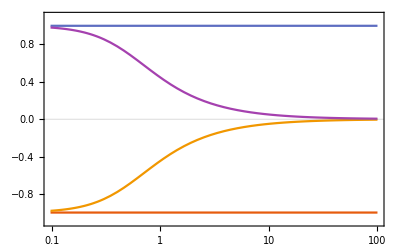

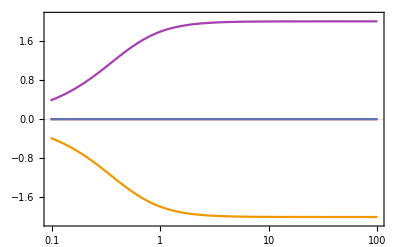

```mathematica
LogLinearPlot[Evaluate@Table[-4vᵀ.zz.v/.h->hh,{v,vecs}],{hh,0,100},PlotRange->1.1{-1,1},PlotTheme->"Scientific"]
LogLinearPlot[Evaluate@Table[-2vᵀ.tf.v/.h->hh,{v,vecs}],{hh,0,100},PlotRange->2.1{-1,1},PlotTheme->"Scientific"]
```

## Heisenberg

```mathematica
xx = KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]/4;
yy = KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]/4;
zz = KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]/4;
tf = KroneckerProduct[PauliMatrix[0],PauliMatrix[1]]/2 + KroneckerProduct[PauliMatrix[1],PauliMatrix[0]]/2;
```

```mathematica
zz//MatrixForm
tf//MatrixForm
```

(1/4 | 0 | 0 | 0
0 | -1/4 | 0 | 0
0 | 0 | -1/4 | 0
0 | 0 | 0 | 1/4)

(0 | 1/2 | 1/2 | 0
1/2 | 0 | 0 | 1/2
1/2 | 0 | 0 | 1/2
0 | 1/2 | 1/2 | 0)

```mathematica
H2=4xx+4yy+4zz -2 h tf;
H2//MatrixForm
{vals,vecs}=Eigensystem[H2];
```

(1 | -h | -h | 0
-h | -1 | 2 | -h
-h | 2 | -1 | -h
0 | -h | -h | 1)

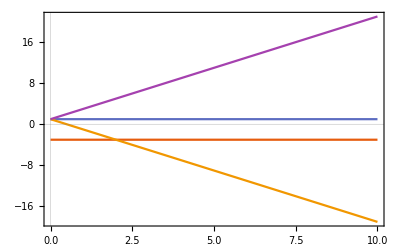

```mathematica
Plot[Evaluate@vals,{h,0,10},PlotTheme->"Scientific"]
```

```mathematica
vecs=(Table[Normalize[v],{v,vecs}]//ComplexExpand//FullSimplify);
```

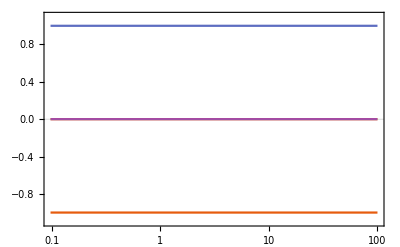

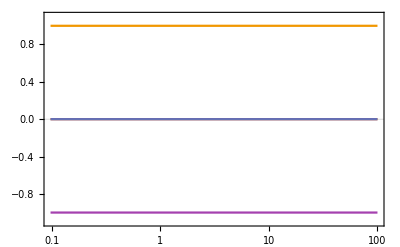

```mathematica
LogLinearPlot[Evaluate@Table[4vᵀ.zz.v/.h->hh,{v,vecs}],{hh,0,100},PlotRange->1.1{-1,1},PlotTheme->"Scientific"]
LogLinearPlot[Evaluate@Table[vᵀ.tf.v/.h->hh,{v,vecs}],{hh,0,100},PlotRange->1.1{-1,1},PlotTheme->"Scientific"]
```

## Power iteration

```mathematica
Clear[powerIteration,A,b0,n]
powerIteration[A_,b0_,n_:2]:=Module[{b,μ,k,abk,norm},
b[0]=b0;
Do[
abk=A.b[k];
norm=b[k]*.b[k];
μ[k]=b[k]*.abk/norm;
b[k+1]=abk/Norm[abk];

,{k,0,n}];
{b,μ}]
```

```mathematica
Clear[λ,A,B,b,μ,bA,μA,bB,μB,nmax]
λ[1]=1.0;λ[2]=.93;
A={{λ[1],0,0,0},{0,λ[2],0,0},{0,0,λ[2],0},{0,0,0,λ[2]}};
A//MatrixForm
B={{λ[1],0,0,0},{0,λ[2],1,0},{0,0,λ[2],1},{0,0,0,λ[2]}};
B//MatrixForm
{bA,μA}=powerIteration[A,{1,1,1,1},nmax=100000];
{bB,μB}=powerIteration[B,{1,1,1,1},nmax];
```

(1. | 0 | 0 | 0
0 | 0.93 | 0 | 0
0 | 0 | 0.93 | 0
0 | 0 | 0 | 0.93)

(1. | 0 | 0 | 0
0 | 0.93 | 1 | 0
0 | 0 | 0.93 | 1
0 | 0 | 0 | 0.93)

```mathematica
1/4{1,1,1,1}†.A.{1,1,1,1}
```

0.9475

```mathematica
ListLogPlot[Table[{Max[Abs[bA[i]-{1,0,0,0}]], Max[Abs[bB[i]-{1,0,0,0}]]},{i,0,nmax}]ᵀ,Joined->True,PlotRange->Full];
Show[ListLogPlot[Table[{k,200000(λ[2]/λ[1])^k},{k,1,nmax,nmax/100}],Joined->True,PlotStyle->{Black,Dashed}],%]
```

General::munfl: 0.93^10001 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.93^11001 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.93^12001 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

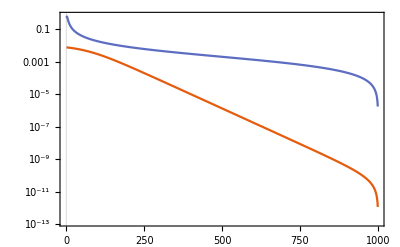

1.

0.991996

```mathematica
ListLogPlot[Table[Abs[{μA[k]-μA[nmax],μB[k]-μB[nmax]}],{k,0,nmax-1}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific"]
μA[nmax]
μB[nmax]
```

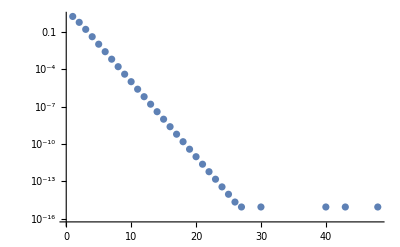

-3.

```mathematica
h=1;μ=1;
{bA,μA}=powerIteration[H2-μ*IdentityMatrix[4],Normalize[RandomReal[{-1,1},4]],nmax=1000];
ListLogPlot[Table[Abs[Min[Evaluate@vals//N]-μA[k]-μ],{k,nmax}]]
μA[nmax]+μ
```

### TFIM -- bigger systems

```mathematica
Clear[S,Ss]
Table[S[i] = SparseArray[0.5*PauliMatrix[i]],{i,0,3}];
S[4] = SparseArray[0.5*(PauliMatrix[1]+ⅈ PauliMatrix[2])];
S[5] = SparseArray[0.5*(PauliMatrix[1]-ⅈ PauliMatrix[2])];
Clear[Ss,IDL,IDR,Ns]
generateSpinMatrices[Ns_]:=Module[{Ss,H,V,vals,vecs,order,IDL,IDR},
IDL[l_]:=1.0*SparseArray[IdentityMatrix[2^(l-1)]];
IDR[l_]:=1.0*SparseArray[IdentityMatrix[2^(Ns-l)]];
Table[Ss[l,j]=KroneckerProduct[IDL[l],S[j],IDR[l]],{j,0,5},{l,Ns}];
Ss
]

Clear[powerIterationFast,A,b0,n]
powerIterationFast[A_,b0_,n_:2,tol_:10^-10]:=Module[{bk,μ,k,abk,norm,nsteps,pbk},
bk=b0;
nsteps=-1;
Do[
nsteps+=1;
abk=A.bk;
norm=bk*.bk;
μ[k]=bk*.abk/norm;
pbk=bk;
bk=abk/Norm[abk];
If[Norm[bk-Sign[μ[k]]pbk]<tol, (*Print["Finished after "<>ToString[nsteps]<>" steps."];*) Break[];];

,{k,0,n}];
{bk,μ,nsteps}]
Ss = generateSpinMatrices[nsites=12]
```

Ss$350063

```mathematica
Table[Ss[l,i].Ss[l,j]-Ss[l,j].Ss[l,i]==Sum[Signature[{i,j,k}]*ⅈ*Ss[l,k],{k,3}],{l,1},{i,3},{j,3}]
```

{{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
ns=Table[n,{n,2,18}];
Monitor[
Clear[h,v,nm,ene,mag,corr];
Do[
Ss = generateSpinMatrices[nsites];
zz=Sum[Ss[l,3].Ss[l+1,3],{l,nsites-1}];
tf=Sum[Ss[l,1],{l,nsites}];
Clear[h,HN];
HN[h_]:=-4.0zz -2.0 h tf-10^-2 Sum[Ss[l,3],{l,nsites}];
hs = Table[h,{h,$MachineEpsilon,2,0.01}];
step=0;
Do[
μ=1;
HNm=HN[h];
AbsoluteTiming[{bA,μA,nmax}=powerIterationFast[HNm-μ*IdentityMatrix[2^nsites],Table[1,Length[HNm]],10000,10^-4];];
ListLogPlot[Table[Abs[μA[nmax]-μA[k]],{k,nmax}]];
ene[nsites,step]=bA*.HNm.bA;
Table[mag[nsites,step,s]=1/nsites Sum[bA*.Ss[l,s].bA,{l,nsites}],{s,3}];
(*v[nsites,step]=bA;*)
nm[nsites,step]=nmax;
step+=1;
,{h,hs}];
,{nsites,ns}];,{h,nsites}];
```

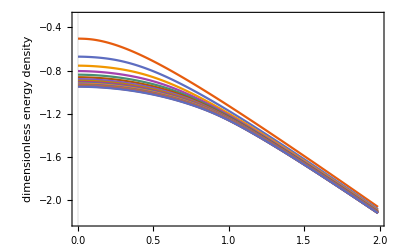

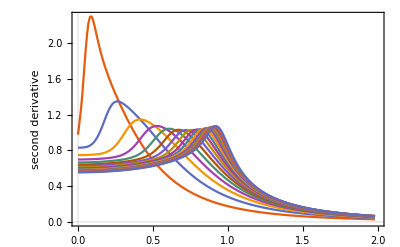

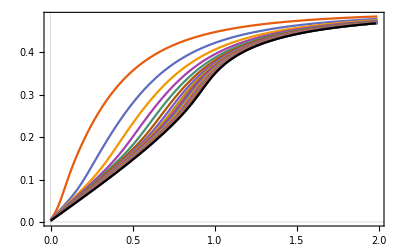

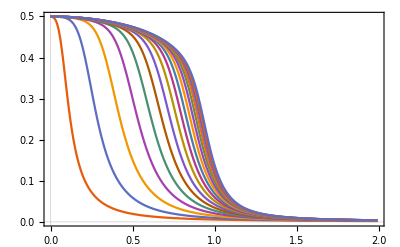

```mathematica
ListPlot[edata=Table[{hs[[nh]],ene[nsites,nh]/nsites},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->{-2.2,-0.3},PlotTheme->"Scientific",FrameLabel->{"","dimensionless energy density "}]
fs=Interpolation[#]&/@edata;
Plot[Evaluate@Table[-fs[[nsites]]''[x],{nsites,Length[ns]}],{x,0,2},PlotTheme->"Scientific",FrameLabel->{"","second derivative "}]

ListPlot[Table[{hs[[nh]],mag[nsites,nh,1]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}];
Show[%,Plot[-0.5*fs[[-1]]'[x],{x,0,2},PlotTheme->"Scientific",PlotStyle->Black]]

ListPlot[magdata=Table[{hs[[nh]],mag[nsites,nh,3]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}]
```

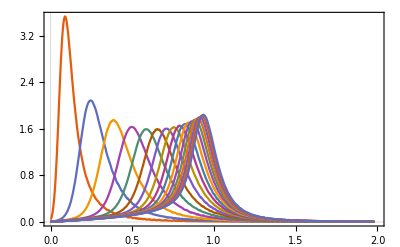

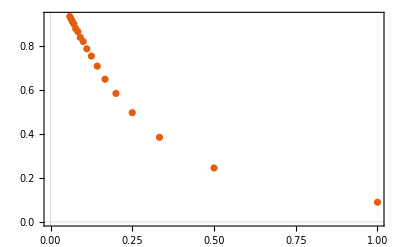

FittedModel[…]

1.06189-2.36556 x

1.06189

```mathematica
fs=Interpolation[#]&/@magdata;
Plot[Evaluate@Table[-fs[[nsites]]'[x],{nsites,Length[ns]}],{x,0,2},PlotRange->Full,PlotTheme->"Scientific"]

ListPlot[maxpos=Table[{1/nsites,x/.FindMaximum[-fs[[nsites]]'[x],{x,0,2}][[2]]},{nsites,Length[ns]}],PlotTheme->"Scientific"]
f=LinearModelFit[maxpos[[4;;]],x,x]
Normal[f]
f[0]
```

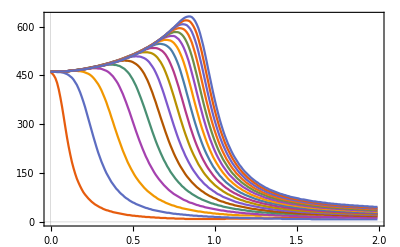

```mathematica
ListPlot[Table[{hs[[nh]],nm[nsites,nh]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}]
```

### Heisenberg -- bigger systems

```mathematica
Clear[S,Ss]
Table[S[i] = SparseArray[0.5*PauliMatrix[i]],{i,0,3}];
S[4] = SparseArray[0.5*(PauliMatrix[1]+ⅈ PauliMatrix[2])];
S[5] = SparseArray[0.5*(PauliMatrix[1]-ⅈ PauliMatrix[2])];
Clear[Ss,IDL,IDR,Ns]
generateSpinMatrices[Ns_]:=Module[{Ss,H,V,vals,vecs,order,IDL,IDR},
IDL[l_]:=1.0*SparseArray[IdentityMatrix[2^(l-1)]];
IDR[l_]:=1.0*SparseArray[IdentityMatrix[2^(Ns-l)]];
Table[Ss[l,j]=KroneckerProduct[IDL[l],S[j],IDR[l]],{j,0,5},{l,Ns}];
Ss
]

Clear[powerIterationFast,A,b0,n]
powerIterationFast[A_,b0_,n_:2,tol_:10^-10]:=Module[{bk,μ,k,abk,norm,nsteps,pbk},
bk=b0;
nsteps=-1;
Do[
nsteps+=1;
abk=A.bk;
norm=bk*.bk;
μ[k]=bk*.abk/norm;
pbk=bk;
bk=abk/Norm[abk];
If[Norm[bk-Sign[μ[k]]pbk]<tol, (*Print["Finished after "<>ToString[nsteps]<>" steps."];*) Break[];];

,{k,0,n}];
{bk,μ,nsteps}]
Ss = generateSpinMatrices[nsites=12]
```

Ss$19857

```mathematica
Table[Ss[l,i].Ss[l,j]-Ss[l,j].Ss[l,i]==Sum[Signature[{i,j,k}]*ⅈ*Ss[l,k],{k,3}],{l,1},{i,3},{j,3}]
```

{{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
ns=Table[n,{n,7,14}];
Monitor[
Clear[h,v,nm,ene,mag,corr];
Do[
Ss = generateSpinMatrices[nsites];
xx=Sum[Ss[l,1].Ss[l+1,1],{l,nsites-1}];
yy=Sum[Ss[l,2].Ss[l+1,2],{l,nsites-1}];
zz=Sum[Ss[l,3].Ss[l+1,3],{l,nsites-1}];
tf=Sum[Ss[l,1],{l,nsites}];
Clear[h,HN];
HN[h_]:=4.0xx+4.0yy+4.0zz -2.0 h tf-10^-2 Sum[Ss[l,3],{l,nsites}];
hs = Table[h,{h,$MachineEpsilon,2,0.01}];
step=0;
Do[
μ=1;
HNm=HN[h];
AbsoluteTiming[{bA,μA,nmax}=powerIterationFast[HNm-μ*IdentityMatrix[2^nsites],Table[1,Length[HNm]],10000,10^-4];];
ListLogPlot[Table[Abs[μA[nmax]-μA[k]],{k,nmax}]];
ene[nsites,step]=bA*.HNm.bA;
Table[mag[nsites,step,s]=1/nsites Sum[bA*.Ss[l,s].bA,{l,nsites}],{s,3}];
(*v[nsites,step]=bA;*)
nm[nsites,step]=nmax;
step+=1;
,{h,hs}];
,{nsites,ns}];,{h,nsites}];
```

$Aborted

```mathematica
ListPlot[edata=Table[{hs[[nh]],ene[nsites,nh]/nsites},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->{-2.2,-0.8},PlotTheme->"Scientific",FrameLabel->{"","dimensionless energy density "}]
fs=Interpolation[#]&/@edata;
Plot[Evaluate@Table[-fs[[nsites]]''[x],{nsites,Length[ns]}],{x,0,2},PlotTheme->"Scientific",FrameLabel->{"","second derivative "}]

ListPlot[Table[{hs[[nh]],mag[nsites,nh,1]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}];
Show[%,Plot[-0.5*fs[[-1]]'[x],{x,0,2},PlotTheme->"Scientific",PlotStyle->Black]]

ListPlot[magdata=Table[{hs[[nh]],mag[nsites,nh,3]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}]
```

```mathematica
fs=Interpolation[#]&/@magdata;
Plot[Evaluate@Table[-fs[[nsites]]'[x],{nsites,Length[ns]}],{x,0,2},PlotRange->Full,PlotTheme->"Scientific"]

ListPlot[maxpos=Table[{1/nsites,x/.FindMaximum[-fs[[nsites]]'[x],{x,0,2}][[2]]},{nsites,Length[ns]}],PlotTheme->"Scientific"]
f=LinearModelFit[maxpos[[4;;]],x,x]
Normal[f]
f[0]
```

```mathematica
ListPlot[Table[{hs[[nh]],nm[nsites,nh]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}]
```